## Basic information;

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
temps4={10,300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
(*At QHA level note -
Vol=> 4.6583 4.685 4.730 4.759 4.801 4.850 is
temps=> 0noZP 754K 1884 2479 3185 3.822
*)
```

```mathematica
qhaVlist={4.6583,4.685,4.730,4.759,4.801,4.850};
qhaTlist={0,754,1884,2479,3185,3822};
```

## Import electron conductivity

```mathematica
(*Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el*)
Import DOS;
(*PRIMTIVE*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaEl={"prim.kp39.465837.trace", "prim.kp39.4685.trace", "prim.kp39.4730.trace", "prim.kp39.4759.trace", "prim.kp39.4801.trace", "prim.kp39.4850.trace"};
(*Exclude the DOS with zero smearing*)
importedPrimTrace=Table[ReadList[filesPrimSigmaEl[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesPrimSigmaEl//Length}];
```

```mathematica
(*DEFECT CONDUCTIVITY.../Volumes/MicroSD/Dropbox/PostDoc_SD/*)
(*-rwxrwxrwx 1 tom staff 1.3M 15 Mar 10:43 prim.kp39.4801.transdos
1 # Ef[Ry] T[K] N DOS(Ef) S s/t R_H kappa0 c chi*)
(*UNITCELL*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el/results_unitcell_sigma_el_kp353535"];
filesUnitSigmaEl={"4.65837a.hte.trace", "4.685a.hte.trace", "4.730a.hte.trace", "4.759a.hte.trace", "4.801a.hte.trace", "4.850a.hte.trace"};
(*Exclude the DOS with zero smearing*)
importedUnitTrace=Table[ReadList[filesUnitSigmaEl[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesPrimSigmaEl//Length}];
```

```mathematica
Import transdos;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaEldos={"prim.kp39.465837.transdos", "prim.kp39.4685.transdos", "prim.kp39.4730.transdos", "prim.kp39.4759.transdos", "prim.kp39.4801.transdos", "prim.kp39.4850.transdos"};
(*Exclude the DOS with zero smearing*)
importedPrimDOS=Table[ReadList[filesPrimSigmaEldos[[i]],{Number,Number,Number}],{i,1,filesPrimSigmaEldos//Length}];
(*1 #DOS(states/Ry/spin)-0.98542411E+00 0.12363563E+01 0.10000000E-03 0.00000000E+00 22218*)
```

```mathematica
(*UNITCELL *)SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el/results_unitcell_sigma_el_kp353535"];
filesUnitSigmaEldos={"4.65837a.hte.transdos", "4.685a.hte.transdos", "4.730a.hte.transdos", "4.759a.hte.transdos", "4.801a.hte.transdos", "4.850a.hte.transdos"};
(*Exclude the DOS with zero smearing*)
importedUnitDOS=Table[ReadList[filesUnitSigmaEldos[[i]],{Number,Number,Number}],{i,1,filesUnitSigmaEldos//Length}];
```

```mathematica
Import v2dos;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaElv2dos={"prim.kp39.465837.v2dos", "prim.kp39.4685.v2dos", "prim.kp39.4730.v2dos", "prim.kp39.4759.v2dos", "prim.kp39.4801.v2dos", "prim.kp39.4850.v2dos"};
(*Exclude the DOS with zero smearing*)
importedPrimv2dos=Table[ReadList[filesPrimSigmaElv2dos[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesPrimSigmaElv2dos//Length}];
(*# Fermi veloc^2/Dos(e)*)
```

```mathematica
(*UNITCELL*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el/results_unitcell_sigma_el_kp353535"];
filesUnitSigmaElv2dos={"4.65837a.hte.v2dos", "4.685a.hte.v2dos", "4.730a.hte.v2dos", "4.759a.hte.v2dos", "4.801a.hte.v2dos", "4.850a.hte.v2dos"};
(*Exclude the DOS with zero smearing*)
importedUnitv2dos=Table[ReadList[filesUnitSigmaElv2dos[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesUnitSigmaElv2dos//Length}];
```

```mathematica
Parse the sigma_el files;
primSIGMAMoTau=Table[Table[{importedPrimTrace[[k]][[i]][[2]],importedPrimTrace[[k]][[i]][[6]]},{i,1,importedPrimTrace[[k]]//Length}][[1;;100]],{k,1,6}];
primKAPPAMoTau=Table[Table[{importedPrimTrace[[k]][[i]][[2]],importedPrimTrace[[k]][[i]][[8]]},{i,1,importedPrimTrace[[k]]//Length}][[1;;100]],{k,1,6}];
primDOS=Table[Table[{importedPrimDOS[[k]][[i]][[1]]*ryd2eV,importedPrimDOS[[k]][[i]][[2]]/ryd2eV},{i,1,importedPrimDOS[[k]]//Length}],{k,1,6}];
primV2DOS=Table[Table[{importedPrimv2dos[[k]][[i]][[1]]*ryd2eV,importedPrimv2dos[[k]][[i]][[2]]/ryd2eV},{i,1,importedPrimv2dos[[k]]//Length}],{k,1,6}];
```

```mathematica
unitSIGMAMoTau=Table[Table[{importedUnitTrace[[k]][[i]][[2]],importedUnitTrace[[k]][[i]][[6]]},{i,1,importedUnitTrace[[k]]//Length}][[1;;100]],{k,1,6}];
unitKAPPAMoTau=Table[Table[{importedUnitTrace[[k]][[i]][[2]],importedUnitTrace[[k]][[i]][[8]]},{i,1,importedUnitTrace[[k]]//Length}][[1;;100]],{k,1,6}];
unitDOS=Table[Table[{importedUnitDOS[[k]][[i]][[1]]*ryd2eV,(1/4)importedUnitDOS[[k]][[i]][[2]]/ryd2eV},{i,1,importedUnitDOS[[k]]//Length}],{k,1,6}];
unitV2DOS=Table[Table[{importedUnitv2dos[[k]][[i]][[1]]*ryd2eV,importedUnitv2dos[[k]][[i]][[2]]/ryd2eV},{i,1,importedUnitv2dos[[k]]//Length}],{k,1,6}];
```

#### Plot DOS v2DOS and sigma/tau;

```mathematica
Show[{ListPlot[primSIGMAMoTau],ListPlot[unitSIGMAMoTau]}]
```

-Graphics-

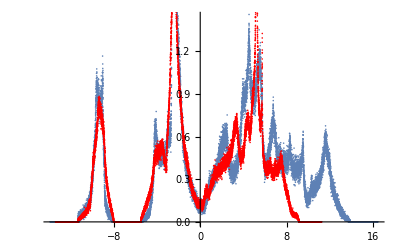

```mathematica
Show[{ListPlot@primDOS[[1]],ListPlot[Transpose[{Transpose[unitDOS[[1]]][[1]],Transpose[unitDOS[[1]]][[2]]}],PlotStyle->Red]}]
```

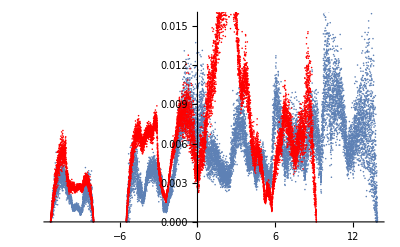

```mathematica
Show[{ListPlot@primV2DOS[[1]],ListPlot[Transpose[{Transpose[unitV2DOS[[1]]][[1]],(1)Transpose[unitV2DOS[[1]]][[2]]}],PlotStyle->Red]}]
```

```mathematica
primSIGMAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[primSIGMAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[primSIGMAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{primSIGMAMoTau[[1]],primSIGMAMoTau[[6]],primSIGMAMoTauInter}]
```

-Graphics-

```mathematica
unitSIGMAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[unitSIGMAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[unitSIGMAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{unitSIGMAMoTau[[1]],unitSIGMAMoTau[[6]],unitSIGMAMoTauInter}]
```

-Graphics-

```mathematica
primKAPPAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[primKAPPAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[primKAPPAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{primKAPPAMoTau[[1]],primKAPPAMoTauInter,primKAPPAMoTau[[6]]}]
```

-Graphics-

```mathematica
unitKAPPAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[unitKAPPAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[unitKAPPAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{unitKAPPAMoTau[[1]],unitKAPPAMoTauInter,unitKAPPAMoTau[[6]]}]
```

-Graphics-

#### Interpolate the DOS

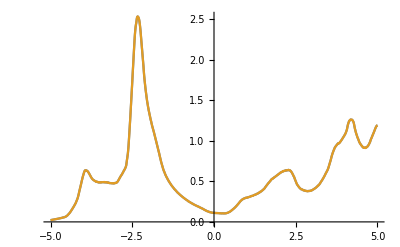

```mathematica
(*Doing a moving average, with window set to temperature*)
windowDOSfun[smearing_]:=(primDOS[[1]]//Length)*smearing/(Last[primDOS[[1]]][[1]]-First[primDOS[[1]]][[1]])*K2eV
DOSwindows=Table[Ceiling[windowDOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
dosWindowInter=Table[Interpolation[MovingAverage[primDOS[[i]],DOSwindows[[i]]]][x],{i,1,primDOS//Length}];
dosWindowInter2=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
Plot[{dosWindowInter[[4]],dosWindowInter2[[4]]},{x,-5,5}]
```

```mathematica
plotOptsDOSinter={Frame->True,PlotRange->{{-5,5},All},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["760 K",18],Style["1900 K",18],Style["2500 K",18],Style["3200 K",18],Style["3800 K",18]}]};

plotOptsDOS={ PlotTheme->"Scientific",PlotStyle->Directive[Orange,Opacity[0.25]],PlotStyle->PointSize[0.03],Frame->True,PlotRange->{{-5,5},All},AspectRatio->1,FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->400};
```

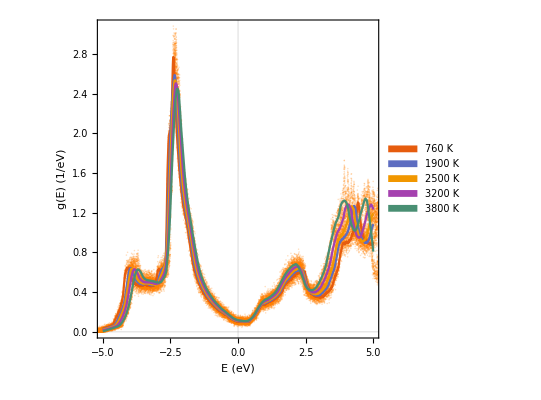

```mathematica
Show[{Table[ListPlot[primDOS[[i]],Evaluate@plotOptsDOS],{i,2,6}],Plot[Evaluate@dosWindowInter[[2;;6]],{x,-5,5},Evaluate@plotOptsDOSinter]}]
```

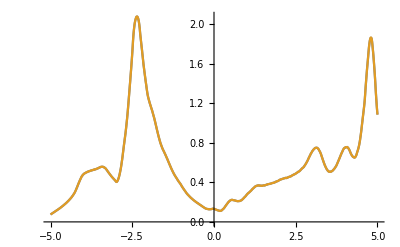

```mathematica
(*Doing a moving average, with window set to temperature*)
unitwindowDOSfun[smearing_]:=(unitDOS[[1]]//Length)*smearing/(Last[unitDOS[[1]]][[1]]-First[unitDOS[[1]]][[1]])*K2eV
unitDOSwindows=Table[Ceiling[unitwindowDOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
unitdosWindowInter=Table[Interpolation[MovingAverage[unitDOS[[i]],unitDOSwindows[[i]]]][x],{i,1,unitDOS//Length}];
unitdosWindowInter2=Table[Interpolation[MovingMap[Mean,unitDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,unitDOS//Length}];
Plot[{unitdosWindowInter[[4]],unitdosWindowInter2[[4]]},{x,-5,5}]
```

#### Look at the variance in ZrC DOS

```mathematica
qhaTlist
qhaTlist2={100,100,100,100,100,100}
qhaTlist4={1000,1000,1000,1000,1000,1000}
qhaTlist3={10,10,10,10,10,10}
```

{0,754,1884,2479,3185,3822}

{100,100,100,100,100,100}

{1000,1000,1000,1000,1000,1000}

{10,10,10,10,10,10}

```mathematica
primDOSinter3=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Max=Table[Interpolation[MovingMap[Max,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Min=Table[Interpolation[MovingMap[Min,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Var=Table[Interpolation[MovingMap[Variance,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
```

Variance::shlen: The argument {0.} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

```mathematica
primDOSinter3100=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist2)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Max100=Table[Interpolation[MovingMap[Max,primDOS[[i]],{K2eV*(qhaTlist2)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Min100=Table[Interpolation[MovingMap[Min,primDOS[[i]],{K2eV*(qhaTlist2)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Var100=Table[Interpolation[MovingMap[Variance,primDOS[[i]],{K2eV*(qhaTlist2)[[i]],Center}]][x],{i,1,primDOS//Length}];
```

```mathematica
primDOSinter310=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist3)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Max10=Table[Interpolation[MovingMap[Max,primDOS[[i]],{K2eV*(qhaTlist3)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Min10=Table[Interpolation[MovingMap[Min,primDOS[[i]],{K2eV*(qhaTlist3)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Var10=Table[Interpolation[MovingMap[Variance,primDOS[[i]],{K2eV*(qhaTlist3)[[i]],Center}]][x],{i,1,primDOS//Length}];
```

Variance::shlen: The argument {0.} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

```mathematica
primDOSinter31000=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Max1000=Table[Interpolation[MovingMap[Max,primDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primDOS//Length}];
primDOSinter3Min1000=Table[Interpolation[MovingMap[Min,primDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,prim//Length}];
primDOSinter3Var1000=Table[Interpolation[MovingMap[Variance,primDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primDOS//Length}];
```

```mathematica
unitDOSinter31000=Table[Interpolation[MovingMap[Mean,unitDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,unitDOS//Length}];
unitDOSinter3Max1000=Table[Interpolation[MovingMap[Max,unitDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,unitDOS//Length}];
unitDOSinter3Min1000=Table[Interpolation[MovingMap[Min,unitDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,unitDOS//Length}];
unitDOSinter3Var1000=Table[Interpolation[MovingMap[Variance,unitDOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,unitDOS//Length}];
```

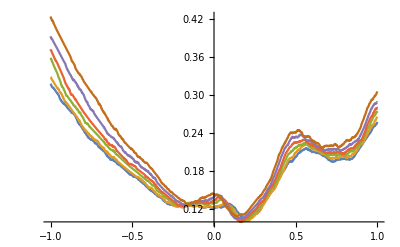

```mathematica
Plot[unitDOSinter31000,{x,-1,1}]
```

```mathematica
pOptsDOS={Frame->True,PlotRange->{{-0.3,0.3},{0.08,0.18}},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->600};
pOptsDOS2={Frame->True,PlotRange->{{-1,1},All},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->600};
pOptsDOS3={Frame->True,PlotRange->{{-10,10},All},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->600};
```

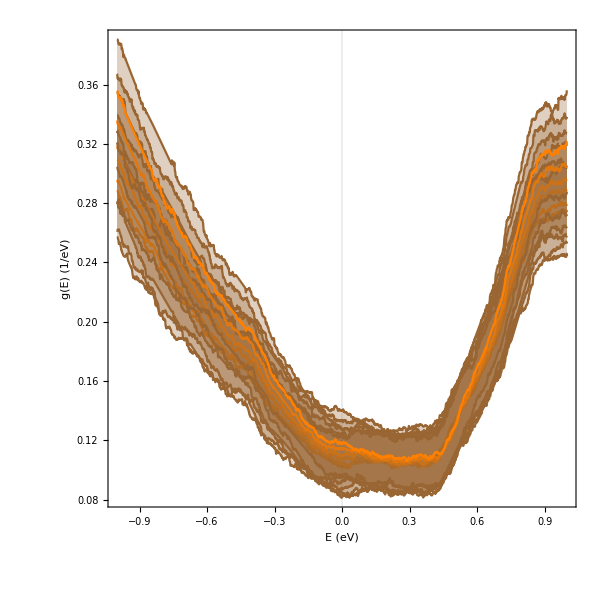

```mathematica
Show@Table[With[{size=i},Plot[{Evaluate[primDOSinter31000[[size]]],Evaluate[primDOSinter31000[[size]]+primDOSinter3Var1000[[size]]^0.5],Evaluate[primDOSinter31000[[size]]-primDOSinter3Var1000[[size]]^0.5]},{x,-1,1},Filling->{2->{3}},PlotStyle->{Orange,Brown,Brown},Evaluate@pOptsDOS2]],{i,1,6}]
```

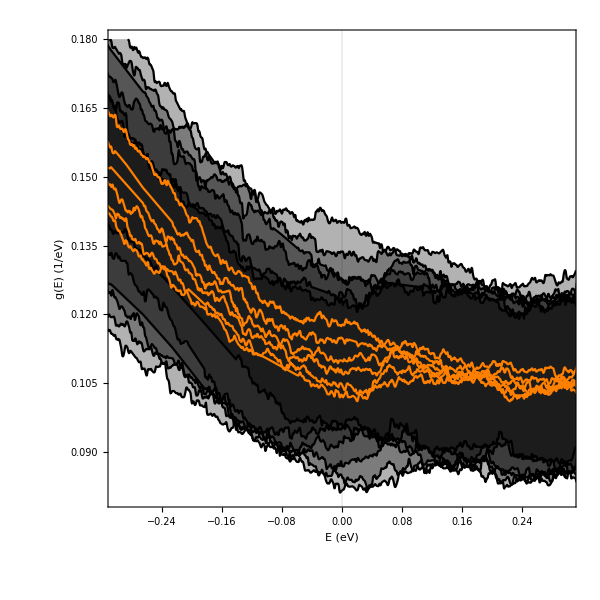

```mathematica
Show[{Table[With[{size=i},Plot[{Evaluate[primDOSinter31000[[size]]+primDOSinter3Var1000[[size]]^0.5],Evaluate[primDOSinter31000[[size]]-primDOSinter3Var1000[[size]]^0.5]},{x,-1,1},Filling->{1->{2}},PlotStyle->{Black},Evaluate@pOptsDOS]],{i,1,6}],Table[With[{size=i},Plot[Evaluate[primDOSinter31000[[size]]],{x,-1,1},Evaluate@pOptsDOS,PlotStyle->{Orange}]],{i,1,6}]}]
```

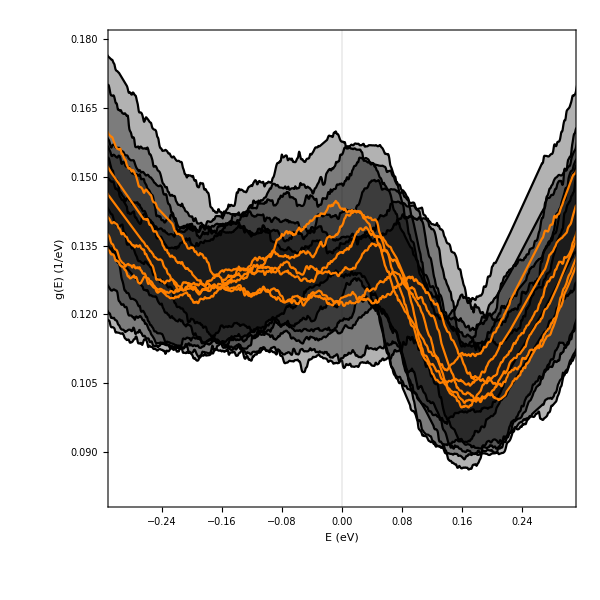

```mathematica
Show[{Table[With[{size=i},Plot[{Evaluate[unitDOSinter31000[[size]]+unitDOSinter3Var1000[[size]]^0.5],Evaluate[unitDOSinter31000[[size]]-unitDOSinter3Var1000[[size]]^0.5]},{x,-1,1},Filling->{1->{2}},PlotStyle->{Black},Evaluate@pOptsDOS]],{i,1,6}],Table[With[{size=i},Plot[Evaluate[unitDOSinter31000[[size]]],{x,-1,1},Evaluate@pOptsDOS,PlotStyle->{Orange}]],{i,1,6}]}]
```

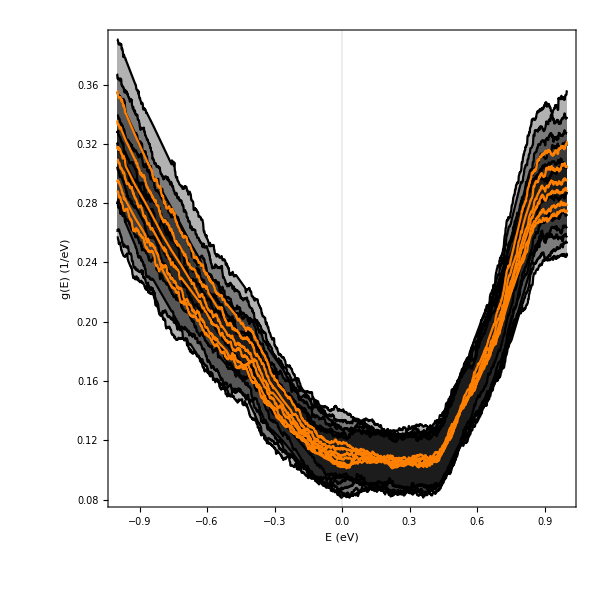

```mathematica
Show[{Table[With[{size=i},Plot[{Evaluate[primDOSinter31000[[size]]+primDOSinter3Var1000[[size]]^0.5],Evaluate[primDOSinter31000[[size]]-primDOSinter3Var1000[[size]]^0.5]},{x,-1,1},Filling->{1->{2}},PlotStyle->{Black},Evaluate@pOptsDOS2]],{i,1,6}],Table[With[{size=i},Plot[Evaluate[primDOSinter31000[[size]]],{x,-1,1},Evaluate@pOptsDOS2,PlotStyle->{Orange}]],{i,1,6}]}]
```

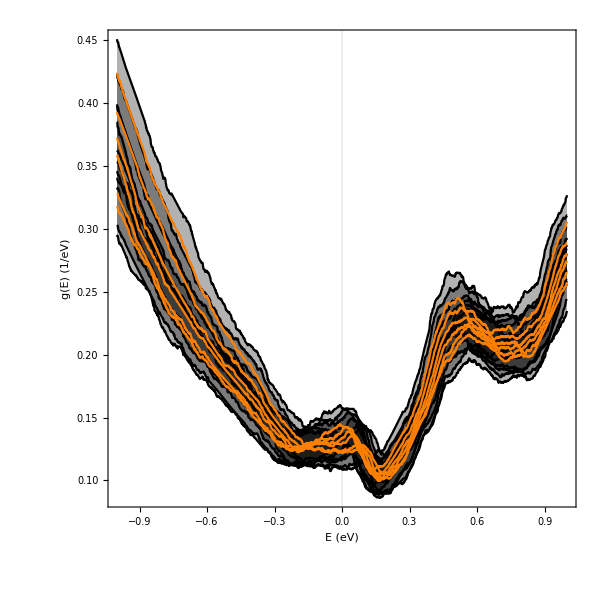

```mathematica
Show[{Table[With[{size=i},Plot[{Evaluate[unitDOSinter31000[[size]]+unitDOSinter3Var1000[[size]]^0.5],Evaluate[unitDOSinter31000[[size]]-unitDOSinter3Var1000[[size]]^0.5]},{x,-1,1},Filling->{1->{2}},PlotStyle->{Black},Evaluate@pOptsDOS2]],{i,1,6}],Table[With[{size=i},Plot[Evaluate[unitDOSinter31000[[size]]],{x,-1,1},Evaluate@pOptsDOS2,PlotStyle->{Orange}]],{i,1,6}]}]
```

#### Interpolate the v2DOS;

```mathematica
(*Doing a moving average, with window set to temperature*)
windowV2DOSfun[smearing_]:=(primV2DOS[[1]]//Length)*smearing/(Last[primV2DOS[[1]]][[1]]-First[primV2DOS[[1]]][[1]])*K2eV
v2DOSwindows=Table[Ceiling[windowV2DOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
v2dosWindowInter=Table[Interpolation[MovingAverage[primV2DOS[[i]],v2DOSwindows[[i]]]][x],{i,1,primV2DOS//Length}];
v2dosWindowInter2=Table[Interpolation[MovingMap[Mean,primV2DOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
```

```mathematica
primv2DOSinter31000=Table[Interpolation[MovingMap[Mean,primV2DOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
primv2DOSinter3Max1000=Table[Interpolation[MovingMap[Max,primV2DOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
primv2DOSinter3Min1000=Table[Interpolation[MovingMap[Min,primV2DOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
primv2DOSinter3Var1000=Table[Interpolation[MovingMap[Variance,primV2DOS[[i]],{K2eV*(qhaTlist4)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
```

```mathematica
(*Doing a moving average, with window set to temperature*)
unitwindowV2DOSfun[smearing_]:=(unitV2DOS[[1]]//Length)*smearing/(Last[unitV2DOS[[1]]][[1]]-First[unitV2DOS[[1]]][[1]])*K2eV
unitv2DOSwindows=Table[Ceiling[unitwindowV2DOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
unitv2dosWindowInter=Table[Interpolation[MovingAverage[unitV2DOS[[i]],v2DOSwindows[[i]]]][x],{i,1,unitV2DOS//Length}];
unitv2dosWindowInter2=Table[Interpolation[MovingMap[Mean,unitV2DOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,unitV2DOS//Length}];
```

```mathematica
plotOptsV2DOSinter={Frame->True,PlotRange->{{-5,5},{0,0.012}},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["v^2/g(E)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["760 K",18],Style["1900 K",18],Style["2500 K",18],Style["3200 K",18],Style["3800 K",18]}]};
plotOptsV2DOS={ PlotTheme->"Scientific",PlotStyle->Directive[Orange,Opacity[0.25]],PlotStyle->PointSize[0.03],Frame->True,PlotRange->{{-5,5},{0,0.012}},AspectRatio->1,FrameLabel->{Style["E (eV)",20],Style["v^2/g(E)",20]},FrameTicksStyle->20,ImageSize->400};
```

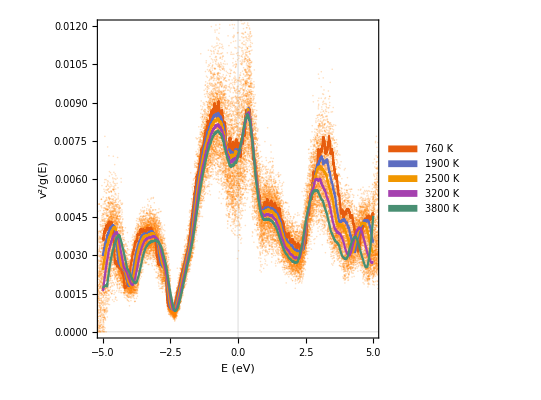

```mathematica
Show[{Table[ListPlot[primV2DOS[[i]],Evaluate@plotOptsV2DOS],{i,2,6}],Plot[Evaluate@v2dosWindowInter[[2;;6]],{x,-5,5},Evaluate@plotOptsV2DOSinter]}]
```

#### Plot DOS times v2DOS

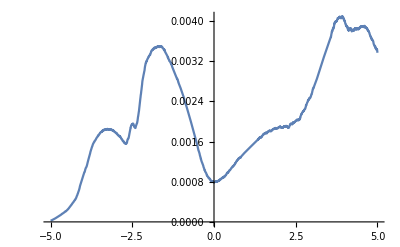

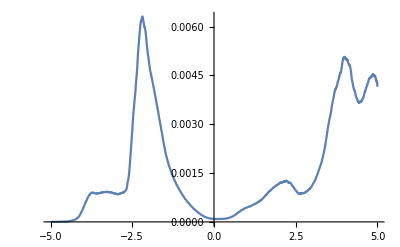

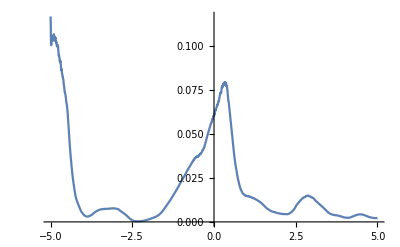

```mathematica
Plot[v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]],{x,-5,5}]
Plot[v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]],{x,-5,5}]
Plot[v2dosWindowInter[[5;;5]]/dosWindowInter[[5;;5]],{x,-5,5}]
```

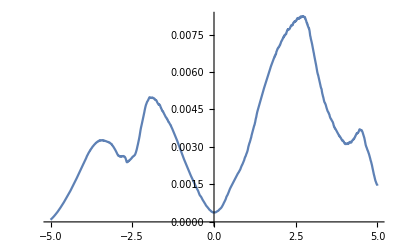

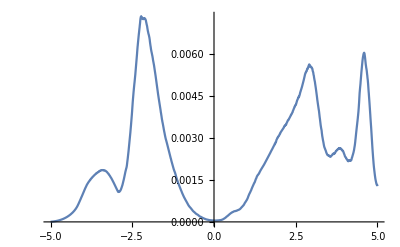

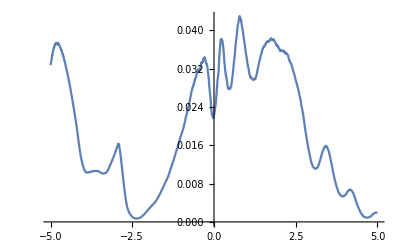

```mathematica
Plot[unitv2dosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]],{x,-5,5}]
Plot[unitv2dosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]],{x,-5,5}]
Plot[unitv2dosWindowInter[[5;;5]]/unitdosWindowInter[[5;;5]],{x,-5,5}]
```

## Scattering Rates;

#### Get scattering Rates;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRates=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

#### Parse rates and lives;

```mathematica
rateData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[scatteringRates[[i]]][[4]]}],{i,1,11}];
lifeData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[1/scatteringRates[[i]]][[4]]}],{i,1,11}];
```

#### Downsample and plot lifetime and scattering rate;

```mathematica
rateDataR6=Table[RandomSample[rateData[[i]],0.15*10^6],{i,1,11}];
rateDataR5=Table[RandomSample[rateData[[i]],10^5],{i,1,11}];
rateDataR4=Table[RandomSample[rateData[[i]],10^4],{i,1,11}];
rateDataR3=Table[RandomSample[rateData[[i]],10^3],{i,1,11}];
rateDataR2=Table[RandomSample[rateData[[i]],10^2],{i,1,11}];
lifeDataR6=Table[RandomSample[lifeData[[i]],0.15*10^6],{i,1,11}];
lifeDataR5=Table[RandomSample[lifeData[[i]],10^5],{i,1,11}];
lifeDataR4=Table[RandomSample[lifeData[[i]],10^4],{i,1,11}];
lifeDataR3=Table[RandomSample[lifeData[[i]],10^3],{i,1,11}];
lifeDataR2=Table[RandomSample[lifeData[[i]],10^2],{i,1,11}];
```

```mathematica
plotOptsRates={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Scattering rate (1/s)",20]},PlotRange->{All,{0,6*10^15}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[PointSize[0.000007]],PlotLegends->SwatchLegend[Table[Style[temps[[i]],20],{i,2,11,2}]]};
plotOptsLives={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Lifetime tau (s)",20]},PlotRange->{{-5,5},{0,5*10^-14}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[PointSize[0.000007]],PlotLegends->SwatchLegend[Table[Style[temps[[i]],20],{i,2,11,2}]]};
```

```mathematica
ListPlot[Table[rateDataR5[[i]],{i,2,11,2}],Evaluate@plotOptsRates]
```

-Graphics-

```mathematica
ListPlot[Table[lifeDataR5[[i]],{i,2,11,2}],Evaluate@plotOptsLives]
```

-Graphics-

```mathematica
tempsScatter={1,10,300,500,760,1000,1500,1900,2500,3200,3800};
tempsScatterMixed300={300,300,300,500,760,1000,1500,1900,2500,3200,3800};
tempsScatterMixed100={100,100,300,500,760,1000,1500,1900,2500,3200,3800};
tempsScatterMixed50={50,50,300,500,760,1000,1500,1900,2500,3200,3800};
```

```mathematica
interRate=Table[Interpolation[MovingMap[Mean,{rateDataR4[[i]]},{K2eV*(tempsScatter[[i]]+1),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(tempsScatter[[i]]+1),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau0010=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(10),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau0100=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(100),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau1000=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(1000),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTauMixed300=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*tempsScatterMixed300[[i]]+1,Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTauMixed100=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*tempsScatterMixed100[[i]]+1,Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTauMixed50=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*tempsScatterMixed50[[i]]+1,Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
K2eV*(tempsScatter)
```

{0.0000861733,0.000861733,0.025852,0.0430867,0.0654917,0.0861733,0.12926,0.163729,0.215433,0.275755,0.327459}

#### Plot lifetime tau;

```mathematica
tauOpts={AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0025]],PlotRange->{{300,3800},Automatic},PlotStyle->Directive[Thickness[0.01]],PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["τ (fs)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400};
```

```mathematica
plotOptsTauRates={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["E-E_F (eV)",20,Black],Style["2Σ'' (PHz)",20,Black]},PlotRange->{All,{0,6}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[Table[Style[temps[[i]],18],{i,1,11}]],{ Right,Top}]};
plotOptsTauRates66={FrameTicksStyle->20,Frame->True,ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["E-E_F (eV)",20,Black],Style["2Σ'' (PHz)",20,Black]},PlotRange->{All,{0,6}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[Table[Style[temps[[i]],18],{i,3,11,2}]],{ 0.65,0.69}]};
plotOptsTauLives={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Lifetime tau (s)",20]},PlotRange->{{-5,5},{0,2.5*10^-14}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[Table[Style[temps[[i+1]],20],{i,1,10}]]};
plotOptsTauLives2={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Lifetime tau (s)",20]},PlotRange->{{-1,1},{0,2.5*10^-14}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[Table[Style[temps[[i+1]],20],{i,1,10}]]};
```

#### Scattering rate with smearing = temperature

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

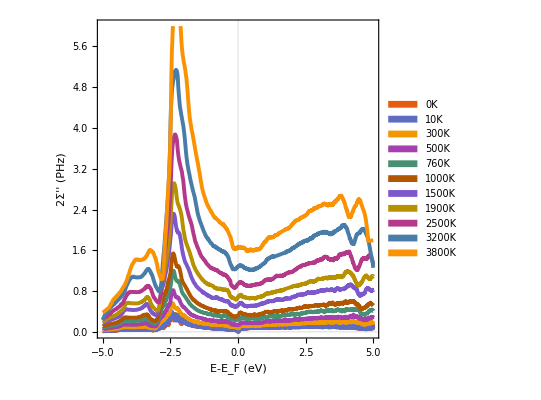

```mathematica
Plot[Evaluate@Table[(10^-15)*interRate[[i]][x],{i,1,11}],{x,-5,5},Evaluate@plotOptsTauRates]
```

```mathematica
Plot[Evaluate@Table[(10^-15)*interRate[[i]][x],{i,3,11,2}],{x,-5,5},Evaluate@plotOptsTauRates66]
```

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
4
```

4

```mathematica
varDat=Table[Interpolation[MovingMap[Mean,MovingMap[StandardDeviation,rateDataR4[[i]],{0.2,Center}],{0.2,Center}],InterpolationOrder->1],{i,1,11}];
```

```mathematica
varDat=Table[Interpolation[MovingMap[Mean,MovingMap[StandardDeviation,rateDataR4[[i]],{0.2,Center}],{0.2,Center}],InterpolationOrder->1],{i,1,11}];
maxDat=Table[Interpolation[MovingMap[Mean,MovingMap[Max,rateDataR4[[i]],{0.2,Center}],{0.2,Center}],InterpolationOrder->1],{i,1,11}];
minDat=Table[Interpolation[MovingMap[Mean,MovingMap[Min,rateDataR4[[i]],{0.2,Center}],{0.2,Center}],InterpolationOrder->1],{i,1,11}];
meanDat=Table[Interpolation[MovingMap[Mean,rateDataR4[[i]],{0.15,Center}],InterpolationOrder->1],{i,1,11}];
```

```mathematica
pRateOpts={FrameTicksStyle->Directive[20,Black,Thickness[0.004]],Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20,Black],Style["2Σ''(ω,T)",20,Black]},PlotRange->{{-4,4},{0,4.6*10^15}},AspectRatio->1,FillingStyle->Opacity[0.2],PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.005]]};
pRateOpts2={Frame->True,FrameTicksStyle->Directive[20,Black,Thickness[0.004]],ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20,Black],Style["2Σ''(ω,T)",20,Black]},PlotRange->{{-4,4},{0,4.6*10^15}},AspectRatio->1,FillingStyle->Opacity[0.5],PlotTheme->"Scientific",PlotStyle->Directive[Black,Thickness[0.001]]};
pRateOpts2a={FrameTicksStyle->Directive[20,Black,Thickness[0.004]],Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20,Black],Style["2Σ''(ω,T)",20],Black},PlotRange->{{-4,4},{0,4.6*10^15}},AspectRatio->1,FillingStyle->Opacity[0.5],PlotTheme->"Scientific",PlotStyle->Directive[Dashing[0.02],Black,Thickness[0.0002]]};
```

```mathematica
Show[{Table[Plot[{maxDat[[i]][x],minDat[[i]][x]},{x,-4,4},Evaluate@pRateOpts2],{i,2,11,3}],ListPlot[Table[rateDataR5[[i]],{i,2,11,3}],PlotTheme->"Scientific",PlotStyle->Opacity[0.4]],Table[Plot[{meanDat[[i]][x]+varDat[[i]][x],meanDat[[i]][x]-varDat[[i]][x]},{x,-4,4},Evaluate@pRateOpts2a,Filling->{1->{2}}],{i,2,11,3}],Plot[Evaluate@Table[meanDat[[i]][x],{i,2,11,3}],{x,-4,4},Evaluate@pRateOpts,PlotLegends->Placed[SwatchLegend[Table[Style[temps[[i]],20],{i,2,11,3}]],{0.63,Top}]]},ImageSize->400]
```

-Graphics-

```mathematica
Show[{ListLinePlot[{maxDat[[7]],minDat[[7]]},Filling->{1->{2}},Evaluate@pRateOpts],ListLinePlot[{meanDat[[7]]},PlotStyle->Orange]}]
```

-Graphics-

```mathematica
Filling->{1->{2}}
```

Filling→{1→{2}}

```mathematica
Show[{ListPlot@MovingMap[Max,rateDataR5[[1]],{0.01,Center}],ListPlot@MovingMap[Max,rateDataR5[[1]],{0.01,Center}]}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

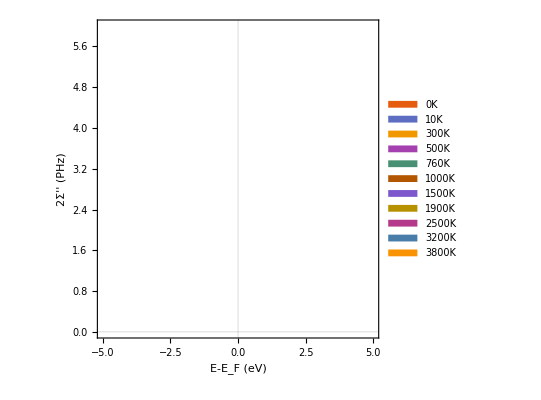

```mathematica
Plot[Evaluate@Table[interRate[[i]][x],{i,1,11}],{x,-5,5},Evaluate@plotOptsTauRates,Filling->True,FillingStyle->Directive[Opacity[0.1]]]
```

#### lifetime with Smearing = temperature

```mathematica
Plot[Evaluate@Table[interTau[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[Evaluate@Table[interTau[[i]][x],{i,2,11}],{x,-1,1},Evaluate@plotOptsTauLives2]
```

-Graphics-

#### 0.01eV smearing

```mathematica
Plot[Evaluate@Table[interTau0010[[i]][x],{i,2,11}],{x,-1,1},Evaluate@plotOptsTauLives2]
```

-Graphics-

```mathematica
0.1eV smearing
```

0.1 eV smearing

```mathematica
Plot[Evaluate@Table[interTau0100[[i]][x],{i,2,11}],{x,-1,1},Evaluate@plotOptsTauLives2]
```

-Graphics-

```mathematica
1eV smearing
```

eV smearing

```mathematica
Plot[Evaluate@Table[interTau1000[[i]][x],{i,2,11}],{x,-1,1},Evaluate@plotOptsTauLives2]
```

-Graphics-

#### Mixed smearing

```mathematica
Plot[Evaluate@Table[interTauMixed100[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives2]
```

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Evaluate@Table[interTauMixed100[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

#### Plot kernel of convolution of lifetime and transport distribution function

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempsScatter[[i]]]*interTau[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-0.2,0.2},All}]
Off[s::Infinity::indet]
```

Part::pkspec1: The expression i cannot be used as a part specification.

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempsScatter[[i]]]*interTauMixed100[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-0.2,0.2},All}]
Off[s::Infinity::indet]
```

Part::pkspec1: The expression i cannot be used as a part specification.

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempsScatter[[i]]]*interTau1000[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-0.2,0.2},All}]
Off[s::Infinity::indet]
```

Part::pkspec1: The expression i cannot be used as a part specification.

InterpolatingFunction::dmval: Input value {-4.9998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
upper=5;lower=-5;
Off[s::NIntegrate::slwcon]
Off[s::General::stop]
Off[s::NIntegrate::eincr]
Off[s::General::stop]
meanTau=Table[(1/NIntegrate[1,{energy,-5,5}])*NIntegrate[interTau[[i]][energy],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
(*Note delta_T=1 added to the integral over f' to make it stable*)
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
meanTauFD=Table[(1/NIntegrate[sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*sigmaK[energy,tempps[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.56231×10^-13 and 1.77758×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.79185×10^-14 and 3.30303×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.14986×10^-14 and 1.15752×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{1.56231×10^-14,7.79185×10^-15,5.14986×10^-15,3.44457×10^-15,2.62851×10^-15,1.72282×10^-15,1.36217×10^-15,1.00502×10^-15,7.79065×10^-16,6.03016×10^-16}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.81832×10^-13 and 8.26536×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32392×10^-14 and 8.78987×10^-30 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.84941×10^-15 and 1.09273×10^-27 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{9.63579×10^-13,1.32392×10^-14,6.84941×10^-15,4.12807×10^-15,3.09776×10^-15,1.93134×10^-15,1.47784×10^-15,1.06242×10^-15,7.59856×10^-16,5.60924×10^-16}

```mathematica
meanTauFD0010=Table[(1/NIntegrate[sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau0010[[i]][energy]*sigmaK[energy,tempps[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.81832×10^-13 and 8.26536×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.33717×10^-14 and 4.52869×10^-28 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.83756×10^-15 and 8.80428×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{9.63579×10^-13,1.33717×10^-14,6.83756×10^-15,4.12383×10^-15,3.12533×10^-15,1.9379×10^-15,1.48232×10^-15,1.07345×10^-15,7.67868×10^-16,5.60681×10^-16}

```mathematica
tempps
```

{0,10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
fv2dos0=(v2dosWindowInter[[5;;5]])/.x->energy;
fv2dos1=(v2dosWindowInter[[5;;5]]/dosWindowInter[[5;;5]])/.x->energy;
fv2dos2=(v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]])/.x->energy;
fv2dos3=(v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]])/.x->energy;
```

```mathematica
unitfv2dos0=(unitv2dosWindowInter[[5;;5]])/.x->energy;
unitfv2dos1=(unitv2dosWindowInter[[5;;5]]/unitdosWindowInter[[5;;5]])/.x->energy;
unitfv2dos2=(unitv2dosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]])/.x->energy;
unitfv2dos3=(unitv2dosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]]*unitdosWindowInter[[5;;5]])/.x->energy;
```

```mathematica
meanTauFDv2f1=Table[(1/NIntegrate[fv2dos1*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos1*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.0300297 and 0.00243266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.89541×10^-14 and 2.36091×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0607001 and 0.0000330577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.02068×10^-16 and 3.23882×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0607487 and 0.0000376069 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.15322×10^-16 and 1.28829×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{9.64184×10^-13},{1.32136×10^-14},{6.83671×10^-15},{4.10891×10^-15},{3.08368×10^-15},{1.9317×10^-15},{1.48575×10^-15},{1.07791×10^-15},{7.77695×10^-16},{5.80099×10^-16}}

```mathematica
meanTauFDv2f2=Table[(1/NIntegrate[fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.000395568 and 0.0000322716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.80542×10^-16 and 2.98423×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000800607 and 2.4299×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05896×10^-17 and 3.90255×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000809541 and 2.44608×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.53973×10^-18 and 2.39695×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{9.62016×10^-13},{1.3227×10^-14},{6.84305×10^-15},{4.1234×10^-15},{3.09295×10^-15},{1.91967×10^-15},{1.46028×10^-15},{1.03314×10^-15},{7.29642×10^-16},{5.31683×10^-16}}

```mathematica
meanTauFDv2f3=Table[(1/NIntegrate[fv2dos3*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos3*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.0000453701 and 3.68263×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.36265×10^-17 and 3.6331×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0196867}. NIntegrate obtained 0.0000920389 and 3.53043×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.21774×10^-18 and 8.47835×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0196867}. NIntegrate obtained 0.0000937551 and 3.82922×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.41732×10^-19 and 5.60274×10^-27 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{9.61569×10^-13},{1.32307×10^-14},{6.84477×10^-15},{4.12831×10^-15},{3.09229×10^-15},{1.90176×10^-15},{1.43086×10^-15},{9.85955×10^-16},{6.7418×10^-16},{4.74941×10^-16}}

```mathematica
meanTauFDv2f0Mixed100=Table[(1/NIntegrate[fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTauMixed100[[i]][energy]*fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00344042 and 0.000279753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65489×10^-16 and 2.04941×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00696935 and 3.62873×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.56137×10^-17 and 1.35981×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00700537 and 2.68054×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.12122×10^-17 and 2.10497×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{4.81013×10^-14},{9.4146×10^-15},{5.88295×10^-15},{3.81232×10^-15},{2.93523×10^-15},{1.85884×10^-15},{1.43333×10^-15},{1.01935×10^-15},{7.31829×10^-16},{5.43488×10^-16}}

```mathematica
unitmeanTauFDv2f0Mixed100=Table[(1/NIntegrate[unitfv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTauMixed100[[i]][energy]*unitfv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00145799 and 0.000119775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.9962×10^-17 and 9.77253×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00300349 and 5.2282×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.82804×10^-17 and 1.09452×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00316584 and 7.03379×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.86195×10^-17 and 1.4884×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{4.79854×10^-14},{9.41585×10^-15},{5.88137×10^-15},{3.80807×10^-15},{2.92626×10^-15},{1.84695×10^-15},{1.42246×10^-15},{1.00776×10^-15},{7.21774×10^-16},{5.3679×10^-16}}

```mathematica
meanTauFDv2f0Mixed50=Table[(1/NIntegrate[fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTauMixed50[[i]][energy]*fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00344042 and 0.000279753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65741×10^-16 and 2.03199×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00696935 and 3.62873×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.56137×10^-17 and 1.35981×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00700537 and 2.68054×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.12122×10^-17 and 2.10497×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{4.81747×10^-14},{9.4146×10^-15},{5.88295×10^-15},{3.81232×10^-15},{2.93523×10^-15},{1.85884×10^-15},{1.43333×10^-15},{1.01935×10^-15},{7.31829×10^-16},{5.43488×10^-16}}

```mathematica
meanTauFD1000fv2dos0=Table[(1/NIntegrate[fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau1000[[i]][energy]*fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00344042 and 0.000279753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.27393×10^-16 and 5.09071×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00696935 and 3.62873×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.12724×10^-17 and 1.22596×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00700537 and 2.68054×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.78318×10^-17 and 2.47241×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{2.40492×10^-13},{1.30963×10^-14},{6.82788×10^-15},{4.11681×10^-15},{3.08995×10^-15},{1.93127×10^-15},{1.47946×10^-15},{1.06371×10^-15},{7.64746×10^-16},{5.64057×10^-16}}

```mathematica
meanTauFD1000fv2dos2=Table[(1/NIntegrate[fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau1000[[i]][energy]*fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.000395568 and 0.0000322716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.48472×10^-17 and 5.54235×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000800607 and 2.4299×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04897×10^-17 and 2.75242×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000809541 and 2.44608×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.52962×10^-18 and 2.29179×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{2.39775×10^-13},{1.31021×10^-14},{6.83056×10^-15},{4.12392×10^-15},{3.09299×10^-15},{1.92259×10^-15},{1.46275×10^-15},{1.03528×10^-15},{7.33384×10^-16},{5.33183×10^-16}}

```mathematica
UnitmeanTauFD1000fv2dos2=Table[(1/NIntegrate[unitfv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau1000[[i]][energy]*unitfv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.0001898 and 0.0000155596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.5633×10^-17 and 5.57013×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000388582 and 1.24497×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.07633×10^-18 and 2.1777×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000407952 and 1.27893×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.77531×10^-18 and 1.41659×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{2.40427×10^-13},{1.30637×10^-14},{6.80302×10^-15},{4.10423×10^-15},{3.08149×10^-15},{1.9139×10^-15},{1.45577×10^-15},{1.02127×10^-15},{7.2211×10^-16},{5.28845×10^-16}}

```mathematica
UnitmeanTauFD1000fv0dos2=Table[(1/NIntegrate[unitfv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau1000[[i]][energy]*unitfv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00145799 and 0.000119775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.49775×10^-16 and 4.595×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00300349 and 5.2282×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.91753×10^-17 and 1.38728×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.00316584 and 7.03379×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.15151×10^-17 and 2.24443×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{2.39903×10^-13},{1.30433×10^-14},{6.79602×10^-15},{4.09882×10^-15},{3.08329×10^-15},{1.92743×10^-15},{1.47151×10^-15},{1.04728×10^-15},{7.52238×10^-16},{5.56362×10^-16}}

```mathematica
meanTauFD1000=Table[(1/NIntegrate[sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau1000[[i]][energy]*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.20114×10^-13 and 7.01692×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31124×10^-14 and 5.48149×10^-30 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.83649×10^-15 and 4.46022×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{2.40206×10^-13,1.31124×10^-14,6.83649×10^-15,4.12858×10^-15,3.0978×10^-15,1.93413×10^-15,1.48049×10^-15,1.06518×10^-15,7.64572×10^-16,5.6273×10^-16}

```mathematica
tempsScatter
```

{1,10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
ListLinePlot[{meanTau[[2;;10]],meanTauFD[[2;;10]],Flatten@meanTauFDv2f0Mixed100[[2;;10]],Flatten@meanTauFD1000[[2;;10]],Flatten@meanTauFD1000fv2dos0[[2;;10]],Flatten@meanTauFD1000fv2dos2[[2;;10]],Flatten@UnitmeanTauFD1000fv2dos2[[2;;10]],Flatten@meanTauFDv2f0Mixed50[[2;;10]],Flatten@unitmeanTauFDv2f0Mixed100[[2;;10]]},PlotRange->All,PlotLegends->SwatchLegend[{"meanTau","meanTauFD","meanTauFDv2f0Mixed100","meanTauFD1000","meanTauFD1000fv2dos0","meanTauFD1000fv2dos2","UnitmeanTauFD1000fv2dos2","meanTauFDv2f0Mixed50","unitmeanTauFDv2f0Mixed100"}]]
```

-Graphics-

```mathematica
meanTau[[2]]
```

7.79185×10^-15

```mathematica
ListLinePlot[{meanTau[[2;;10]],meanTauFD[[2;;10]],Flatten@unitmeanTauFDv2f0Mixed100[[2;;10]]},PlotRange->All,PlotLegends->SwatchLegend[{"meanTau","meanTauFD"}]]
```

-Graphics-

```mathematica
tmeanTau=Transpose[{tempsScatter[[2;;11]],meanTau[[1;;10]]}];
tmeanTauFD=Transpose[{tempsScatter[[2;;11]],meanTauFD[[1;;10]]}];
tmeanTauFDmix100=Transpose[{tempsScatter[[2;;11]],Flatten@meanTauFDv2f0Mixed100[[1;;10]]}];
tmeanTauFDmix100unit=Transpose[{tempsScatter[[2;;11]],Flatten@unitmeanTauFDv2f0Mixed100[[1;;10]]}];


(*Interpolation*)
tmeanTauInter=Interpolation[tmeanTau,InterpolationOrder->3];
tmeanTauInterFD=Interpolation[tmeanTauFD,InterpolationOrder->1];
tmeanTauInterFDmix100=Interpolation[tmeanTauFDmix100,InterpolationOrder->1];
tmeanTauInterFDmix100unit=Interpolation[tmeanTauFDmix100unit,InterpolationOrder->1];
```

```mathematica
tmeanTauInter10=Table[{i,tmeanTauInter[i]},{i,10,4000,10}];
tmeanTauInterFD10=Table[{i,tmeanTauInterFD[i]},{i,10,4000,10}];
USED; (*tmeanTauInterFD10mix100;*);
tmeanTauInterFD10mix100=Table[{i,tmeanTauInterFDmix100[i]},{i,10,4000,10}];
tmeanTauInterFD10mix100unit=Table[{i,tmeanTauInterFDmix100unit[i]},{i,10,4000,10}];
Show[{ListPlot[tmeanTauInter,PlotRange->{{500,4000},{0,8*10^-15}}],ListPlot@tmeanTauInter10},{ListPlot@tmeanTauInterFD,ListPlot@tmeanTauInterFD10},{ListPlot@tmeanTauInterFD10mix100},{ListPlot[tmeanTauInterFD10mix100unit,PlotStyle->Yellow]}]
```

InterpolatingFunction::dmval: Input value {3810} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3820} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3830} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3810} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3820} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3830} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3810} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3820} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3830} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3810} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3820} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3830} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
fitPolytau=Fit[tmeanTauInterFD10mix100,{1/x,1/x^2,x},x]
```

-(2.33106×10^-11)/x^2+(2.71887×10^-12)/x+3.0219×10^-21 x

```mathematica
Show[{ListPlot[tmeanTauInterFD10mix100],Plot[Interpolation[MovingMap[Mean,tmeanTauInterFD10mix100,{300,Center}],InterpolationOrder->1][x],{x,300,4000},PlotStyle->Directive[Thickness[0.01],Orange]]}]
```

-Graphics-

#### tau presentable and table for real:;

```mathematica
fTauPresentable=Interpolation[MovingMap[Mean,tmeanTauInterFD10mix100,{200,Center}],InterpolationOrder->1]
fTauPresentableList=Table[{t,fTauPresentable[t]},{t,10,4000,10}];
fitPolytau=Fit[fTauPresentableList,{1/x,1/x^1.000001,Log[x],x},x]
Show[{ListPlot@fTauPresentableList,Plot[fitPolytau,{x,10,4000},PlotStyle->Directive[Thickness[0.01],Orange]]}]
```

InterpolatingFunction[{{110., 3900.}}, <>]

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-(1.22195×10^-6)/x^1.+(1.22194×10^-6)/x+6.98787×10^-19 x-4.82836×10^-16 Log[x]

-Graphics-

```mathematica
tauOpts={AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0025]],PlotRange->{{300,3800},Automatic},PlotStyle->Directive[Thickness[0.01]],PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["τ (fs)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400};
Plot[10^15*fTauPresentable[x],{x,300,3800},Evaluate@tauOpts]
```

-Graphics-

```mathematica
tauOpts={AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.0025]],PlotRange->{{300,3800},Automatic},PlotStyle->Directive[Thickness[0.01]],PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["τ (fs)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400};
Plot[10^15*fTauPresentable[x],{x,300,3800},Evaluate@tauOpts]
```

-Graphics-

```mathematica
plotOptsKappaTotes3={AspectRatio->1,PlotRange->{{10,3800},{0,120}},PlotStyle->Directive[Thickness[0.01]],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["κ (W/m/K)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["κ_total(bulk)",18],Style["κ_total(10μm)",18],Style["κ_total(1μm)",18],Style["κ_total(0.1μm)",18],Style["κ_total(0.01μm)",18],Style["κ_el",18]}],{0.38,0.75}]};Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa},PlotRange->{{100,3800},{0,120}},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0025]],ImageSize->500]
```

Show::gcomb: Could not combine the graphics objects in Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa},PlotRange→{{100,3800},{0,120}},AspectRatio→0.66,FrameStyle→Directive[GrayLevel[0],Thickness[0.0025]],ImageSize→500].

Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa},PlotRange→{{100,3800},{0,120}},AspectRatio→0.66,FrameStyle→Directive[GrayLevel[0],Thickness[0.0025]],ImageSize→500]

```mathematica
primSIGMAMoTauInter10=Table[{i,Interpolation[primSIGMAMoTauInter][i]},{i,10,4000,10}];
primSIGMAMoTau300Inter10=Table[{i,Interpolation[primSIGMAMoTau[[2]]][i]},{i,10,4000,10}];
primSIGMAMoTau3800Inter10=Table[{i,Interpolation[primSIGMAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{primSIGMAMoTauInter,primSIGMAMoTau300Inter10,primSIGMAMoTau3800Inter10}],Plot[Interpolation[primSIGMAMoTauInter][x],{x,1,4000}]}]

unitSIGMAMoTauInter10=Table[{i,Interpolation[unitSIGMAMoTauInter][i]},{i,10,4000,10}];
unitSIGMAMoTau300Inter10=Table[{i,Interpolation[unitSIGMAMoTau[[2]]][i]},{i,10,4000,10}];
unitSIGMAMoTau3800Inter10=Table[{i,Interpolation[unitSIGMAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{unitSIGMAMoTauInter,unitSIGMAMoTau300Inter10,unitSIGMAMoTau3800Inter10}],Plot[Interpolation[unitSIGMAMoTauInter][x],{x,1,4000}]}]
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
primKAPPAMoTauInter10=Table[{i,Interpolation[primKAPPAMoTauInter][i]},{i,10,4000,10}];
primKAPPAMoTau300Inter10=Table[{i,Interpolation[primKAPPAMoTau[[2]]][i]},{i,10,4000,10}];
primKAPPAMoTau3800Inter10=Table[{i,Interpolation[primKAPPAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{primKAPPAMoTauInter,primKAPPAMoTau300Inter10,primKAPPAMoTau3800Inter10}],Plot[Interpolation[primKAPPAMoTauInter][x],{x,1,4000}]}]

unitKAPPAMoTauInter10=Table[{i,Interpolation[unitKAPPAMoTauInter][i]},{i,10,4000,10}];
unitKAPPAMoTau300Inter10=Table[{i,Interpolation[unitKAPPAMoTau[[2]]][i]},{i,10,4000,10}];
unitKAPPAMoTau3800Inter10=Table[{i,Interpolation[unitKAPPAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{unitKAPPAMoTauInter,unitKAPPAMoTau300Inter10,unitKAPPAMoTau3800Inter10}],Plot[Interpolation[unitKAPPAMoTauInter][x],{x,1,4000}]}]
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
plotOptsSigma={PlotRange->{{300,3800},{0,3000000}},AspectRatio->0.5,
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["(σ/τ)⟨τ⟩_1",18],Style["(σ/τ)⟨τ⟩_FD",18]}]};
plotSigma1=ListLinePlot[{Transpose[{Transpose[tmeanTauInter10][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInter10][[2]]}],Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10][[2]]}]},Evaluate@plotOptsSigma]
```

-Graphics-

```mathematica
plotSigma1=ListLinePlot[{Transpose[{Transpose[tmeanTauInter10][[1]],Transpose[unitSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInter10][[2]]}],Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[unitSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10][[2]]}]},Evaluate@plotOptsSigma]
```

-Graphics-

### new sigma el data

```mathematica
sigmaZrCdata2=Transpose[{Transpose[tmeanTauInterFD10mix100][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10mix100][[2]]}];
sigmaZrCdataSmooth2=MovingMap[Mean,sigmaZrCdata2,{300,Center}];
ListPlot[{sigmaZrCdata2,sigmaZrCdataSmooth2}]
```

-Graphics-

```mathematica
ListPlot@unitSIGMAMoTauInter10
```

-Graphics-

```mathematica
unitsigmaZrCdata2=Transpose[{Transpose[tmeanTauInterFD10mix100unit][[1]],Transpose[unitSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10mix100unit][[2]]}];
unitsigmaZrCdataSmooth2=MovingMap[Mean,unitsigmaZrCdata2,{300,Center}];
ListPlot[{unitsigmaZrCdata2,unitsigmaZrCdataSmooth2}]
```

-Graphics-

#### Plot sigma el

```mathematica
plotOptsSigma2={PlotRange->{{300,3800},{0,10^-6*2000000}},AspectRatio->0.66,PlotStyle->Thickness[0.012],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["ZrC - Boltztrap UC \n (σ/τ)⟨τ⟩_FD",18]}]};
plotOptsSigma3={PlotRange->{{300,3800},{0,10^-6*2000000}},AspectRatio->0.66,PlotStyle->Directive[Thickness[0.012],Black],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["σ (1/Ω/m)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400,PlotLegends->Placed[{Style["Bloch",18]},{Right,Top}]};
ListLinePlot[{sigmaZrCdataSmooth2/.axisScale,unitsigmaZrCdataSmooth2/.axisScale},Evaluate@plotOptsSigma2]
plotSigmaMe2=ListLinePlot[{unitsigmaZrCdataSmooth2/.axisScale},Evaluate@plotOptsSigma2]
plotSigmaMe3=ListLinePlot[{sigmaZrCdataSmooth2/.axisScale},Evaluate@plotOptsSigma3]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
primKAPPAMoTauInter10[[1;;10]]
tmeanTauInterFD10mix100[[1;;10]]
ListPlot@primKAPPAMoTauInter10[[1;;100]]
polyTauList=Table[{i,fitPolytau/.x->i},{i,10,4000,10}];
Show[{ListPlot@tmeanTauInterFD10mix100[[1;;200]],ListPlot@polyTauList}]

unitKAPPAMoTauInter10[[1;;10]]
tmeanTauInterFD10mix100unit[[1;;10]]
ListPlot@unitKAPPAMoTauInter10[[1;;100]]
polyTauList=Table[{i,fitPolytau/.x->i},{i,10,4000,10}];
Show[{ListPlot@tmeanTauInterFD10mix100unit[[1;;200]],ListPlot@polyTauList}]
```

{{10,3.0499×10^13},{20,7.01765×10^13},{30,1.0986×10^14},{40,1.4956×10^14},{50,1.89286×10^14},{60,2.29048×10^14},{70,2.68857×10^14},{80,3.08723×10^14},{90,3.48657×10^14},{100,3.88667×10^14}}

{{10,4.81013×10^-14},{20,4.67673×10^-14},{30,4.54333×10^-14},{40,4.40992×10^-14},{50,4.27652×10^-14},{60,4.14312×10^-14},{70,4.00972×10^-14},{80,3.87631×10^-14},{90,3.74291×10^-14},{100,3.60951×10^-14}}

-Graphics-

-Graphics-

{{10,3.82197×10^13},{20,6.61971×10^13},{30,9.39449×10^13},{40,1.2152×10^14},{50,1.48979×10^14},{60,1.76379×10^14},{70,2.03778×10^14},{80,2.31231×10^14},{90,2.58796×10^14},{100,2.86529×10^14}}

{{10,4.79854×10^-14},{20,4.66554×10^-14},{30,4.53254×10^-14},{40,4.39955×10^-14},{50,4.26655×10^-14},{60,4.13355×10^-14},{70,4.00055×10^-14},{80,3.86755×10^-14},{90,3.73455×10^-14},{100,3.60155×10^-14}}

-Graphics-

-Graphics-

#### Plot kappa_el

```mathematica
kappaZrCdata2=Transpose[{Transpose[polyTauList][[1]],Transpose[primKAPPAMoTauInter10][[2]]*Transpose[polyTauList][[2]]}];
kappaZrCdataSmooth2=MovingMap[Mean,kappaZrCdata2,{20,Center}];
ListPlot[{kappaZrCdata2,kappaZrCdataSmooth2}]

unitkappaZrCdata2=Transpose[{Transpose[polyTauList][[1]],Transpose[unitKAPPAMoTauInter10][[2]]*Transpose[polyTauList][[2]]}];
unitkappaZrCdataSmooth2=MovingMap[Mean,unitkappaZrCdata2,{20,Center}];
ListPlot[{unitkappaZrCdata2,unitkappaZrCdataSmooth2}]
```

-Graphics-

-Graphics-

```mathematica
ListPlot@primKAPPAMoTauInter10
```

-Graphics-

#### Plot kappa

```mathematica
plotOptsSigma2={PlotRange->{{300,3800},{0,2000000}},AspectRatio->0.66,PlotStyle->Thickness[0.012],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["ZrC - Mellan 2017 \n (σ/τ)⟨τ⟩_FD",18]}]};
```

```mathematica
primKAPPAMoTauInter10=Table[{i,Interpolation[primKAPPAMoTauInter][i]},{i,10,4000,10}];

plotOptsKappa={AspectRatio->0.66,PlotRange->{{10,3800},{0,33}},
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["ZrC - Mellan 2017 \n (κ/τ)⟨τ⟩_FD",18]}]};

ListPlot[{kappaZrCdata2,unitkappaZrCdata2},Evaluate@plotOptsKappa]
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

#### Import experimental sigma_el

```mathematica
SetDirectory["/Users/tom/Documents/ZrC_experimental_sigma/"];
filesExpSigma={"Samsonov_ZrC.txt", "Grossman_ZrC.txt", "Neshpoor_ZrC.txt", "Taylor_ZrC0.94.txt"};
(*Exclude the DOS with zero smearing*)
ExpSigmaRaw=Table[ReadList[filesExpSigma[[i]],{Number,Number}],{i,1,filesExpSigma//Length}];
```

#### Crocombette theoretical data

```mathematica
rhoCroc={7.6543*10^-7,1.0555*10^-6,1.2187*10^-6,1.4876*10^-6,1.7301*10^-6};
sigmElCroc=1/rhoCroc;
tempsCroc={1000,1500,2000,2500,3000};
sigmaCroc=Transpose[{tempsCroc,sigmElCroc}]
plotCrocSigma=ListPlot[sigmaCroc/.axisScale,PlotStyle->Directive[PointSize[0.025],Brown],PlotTheme->"Scientific",PlotLegends->Placed[{Style["Crocombette '13",18]},{Right,Top}]]
```

{{1000,1.30646×10^6},{1500,947418.},{2000,820546.},{2500,672224.},{3000,578001.}}

ReplaceAll::reps: {axisScale} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::lpn: {{1000.,1.30646×10^6},{1500.,947418.},{2000.,820546.},{2500.,672224.},{3000.,578001.}}/.axisScale is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{1000,1.30646×10^6},{1500,947418.},{2000,820546.},{2500,672224.},{3000,578001.}}/.axisScale,PlotStyle→Directive[PointSize[0.025],RGBColor[0.6, 0.4, 0.2]],PlotTheme→Scientific,PlotLegends→Placed[{Crocombette '13},{Right,Top}]]

#### Grossman data exp

```mathematica
rhogGrossman[T_]:=1/(((0.393*10^-4)+(0.767*10^-7)*T)/100)
pGross=Plot[(10^-6)*rhogGrossman[T],{T,300,2800},PlotStyle->Directive[Blue,Thickness[0.012],Dashing[0.03]],PlotTheme->"Scientific",PlotLegends->Placed[{Style["Grossman '65",18]},{Right,Top}]]
```

-Graphics-

#### Import Savvatimsky

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/Figures_papers/"];
filesSavvat={"savvatimskyDataSigmaEl.dat"};
(*Exclude the DOS with zero smearing*)
ExpSigmaSavvat=Table[ReadList[filesSavvat[[i]],{Number,Number}],{i,1,filesSavvat//Length}][[1]];
```

```mathematica
interSavvat=Interpolation[MovingMap[Mean,ExpSigmaSavvat/.axisScale,{100,Center}],InterpolationOrder->3]
pSavvat=Plot[interSavvat[x],{x,2100,5000},PlotRange->All,PlotTheme->"Scientific", PlotStyle->Directive[Dashing[0.03],Thickness[0.012],Orange],PlotLegends->Placed[{Style["Savvatimsky '17",18]},{Right,Top}]];
p2Savvat=Show[{pSavvat,ListPlot[ExpSigmaSavvat/.axisScale]}]
```

InterpolatingFunction[{{2093.07, 4897.22}}, <>]

-Graphics-

## Import VASP optic sigma el

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/VASP_sigma_el_optical/"];
filesOpticSigma={"prim_sigma_el","unit_sigma_el"};
(*Exclude DOS with zero smearing*)
vaspOpticSigma=Table[ReadList[filesOpticSigma[[i]],{Number,Number,Number,Number,Number,Number,Number}],{i,1,filesOpticSigma//Length}];
```

```mathematica
axisScale={a_,b_}->{a,10^-6*b}
axisScaleSingle={b_->b*10^-6}
```

{a_,b_}→{a,b/1000000}

{b_→b/1000000}

```mathematica
opticPrim[[1]]
```

Part::partd: Part specification opticPrim⟦1⟧ is longer than depth of object.

opticPrim⟦1⟧

```mathematica
opticOpts1={PlotRange->{{100,3800},{0,2}},PlotTheme->"Scientific", PlotStyle->Directive[PointSize[0.03],Thickness[0.012],Green],PlotLegends->{Style["ZrC VASP UC σ(ω→ E_Fermi)",18]}};
opticOpts2={PlotRange->{{100,3800},{0,2}},PlotTheme->"Scientific", PlotStyle->Directive[PointSize[0.03],Thickness[0.012],Blue],PlotLegends->{Style["ZrC VASP PC σ(ω→ E_Fermi)",18]}};
opticPrim=Table[Transpose[{Transpose[vaspOpticSigma[[1]]][[1]],Transpose[vaspOpticSigma[[1]]][[i+1]]}],{i,1,6}];
opticUnit=Table[Transpose[{Transpose[vaspOpticSigma[[2]]][[1]],Transpose[vaspOpticSigma[[2]]][[i+1]]}],{i,1,6}];
interOpticPrim=Table[Interpolation[opticPrim[[i]]]/.axisScale,{i,1,6}];
interOpticUnit=Table[Interpolation[opticUnit[[i]]]/.axisScale,{i,1,6}];
pOptic=Show[{ListPlot[opticUnit,Evaluate@opticOpts1],ListPlot[opticPrim,Evaluate@opticOpts2]}]
```

-Graphics-

```mathematica
Import VASP optic sigma el frequency dependent;
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/VASP_sigma_el_optical/prim_VASPcond_sigma_el/"];
filesOpticSigmaOmega={"cond_all.4.65837a.dat", "cond_all.4.685a.dat", "cond_all.4.730a.dat","cond_all.4.759a.dat","cond_all.4.801a.dat" ,"cond_all.4.850a.dat"};
(*Exclude the DOS with zero smearing*)
vaspOpticSigmaOmega=Table[ReadList[filesOpticSigmaOmega[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesOpticSigmaOmega//Length}];
```

```mathematica
fermiLevel={5.62776540,5.49393845,5.27338709,5.13485307,4.93887446,4.71709863};
```

```mathematica
ListPlot@Transpose[{Transpose[vaspOpticSigmaOmega[[1]]][[1]],Transpose[vaspOpticSigmaOmega[[1]]][[2]]}]
```

-Graphics-

```mathematica
vaspOpticSigmaOmega[[3]]//Length
```

5000

```mathematica
interOpt=Table[Table[Interpolation[DeleteDuplicates[Transpose[{Transpose[vaspOpticSigmaOmega[[vol]]][[1]]-fermiLevel[[vol]],Transpose[vaspOpticSigmaOmega[[vol]]][[i]]}]]][energy],{i,2,11}],{vol,1,6}];
```

```mathematica
interOpt[[1]][[1]]
```

InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy]

```mathematica
Plot[interOpt,{energy,1-fermiLevel[[1]],10.5-fermiLevel[[1]]}]
```

-Graphics-

```mathematica
interOpt[[1]]
1/NIntegrate[sigmaK[energy,tempScatShort[[10]]],{energy,-3.2,3.2}]
Plot[Evaluate@sigmaK[energy,tempScatShort[[10]]],{energy,-3.2,3.2},PlotRange->All]
```

{InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy],InterpolatingFunction[{{-4.99997, 5.00003}}, <>][energy]}

NIntegrate::inumr: The integrand (11604.5 ⅇ^((11604.5 energy)/tempScatShort⟦10⟧))/((1+ⅇ^((11604.5 «6»)/tempScatShort⟦10⟧))^2 tempScatShort⟦10⟧) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.2,3.2}}.

1/NIntegrate[sigmaK[energy,tempScatShort⟦10⟧],{energy,-3.2,3.2}]

Part::partd: Part specification tempScatShort⟦10⟧ is longer than depth of object.

-Graphics-

```mathematica
tempScatShort=tempsScatter[[2;;-1]]
opticCond=Quiet@Table[Table[NIntegrate[Evaluate[interOpt[[vol]][[i]]*sigmaK[energy,tempScatShort[[i]]]],{energy,Evaluate[-15*(tempScatShort[[i]])*K2eV],Evaluate[15*(tempScatShort[[i]])*K2eV]}]/NIntegrate[Evaluate[sigmaK[energy,tempScatShort[[i]]]],{energy,Evaluate[-15*(tempScatShort[[i]])*K2eV],Evaluate[15*(tempScatShort[[i]])*K2eV]}],{i,1,10}],{vol,1,6}];
```

{10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
ListPlot[Table[Transpose[{tempScatShort,opticCond[[i]]*10^-6}],{i,1,6}]]
```

-Graphics-

```mathematica
opticPrimT=Table[Transpose[{tempScatShort,opticCond[[i]]}],{i,1,6}];
```

```mathematica
Plot[Interpolation[opticPrimT[[1]],InterpolationOrder->2][x],{x,1,3000}]
```

InterpolatingFunction::dmval: Input value {1.06127} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
opticPrimT[[1]]
```

{{10,11.9401},{300,2.05808},{500,1.32041},{760,0.882362},{1000,0.704297},{1500,0.495855},{1900,0.412139},{2500,0.332678},{3200,0.275309},{3800,0.230153}}

```mathematica
opticPrimT[[1]]/.axisScale
```

{{10,0.0000119401},{300,2.05808×10^-6},{500,1.32041×10^-6},{760,8.82362×10^-7},{1000,7.04297×10^-7},{1500,4.95855×10^-7},{1900,4.12139×10^-7},{2500,3.32678×10^-7},{3200,2.75309×10^-7},{3800,2.30153×10^-7}}

```mathematica
interOpticPrimSigma=MovingMap[Mean,Table[(1-i/4000)*Interpolation[opticPrimT[[1]],InterpolationOrder->2][i]+(i/4000)*Interpolation[opticPrimT[[6]],InterpolationOrder->1][i],{i,1,4000}],{100,Center}];
Show[{ListPlot[interOpticPrimSigma/.axisScaleSingle],Plot[Interpolation[opticPrimT[[1]]/.axisScale,InterpolationOrder->2][x],{x,1,3000}],Plot[Interpolation[opticPrimT[[6]]/.axisScale,InterpolationOrder->2][x],{x,1,3000},PlotStyle->Red]}]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.06127} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[{ListPlot[opticPrim],ListLinePlot[opticPrimT]}]
```

-Graphics-

```mathematica
{PlotRange->{{300,3800},{0,10^-6*2000000}},AspectRatio->0.66,PlotStyle->Directive[Thickness[0.012],Black],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["σ (1/Ω/m)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["DFT Bloch",18]}],{Right,Top}]};
```

```mathematica
ListLinePlot[interOpticPrimSigma]
```

-Graphics-

```mathematica
pOpticT=ListLinePlot[interOpticPrimSigma,PlotTheme->"Scientific",
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["σ (10^-6/Ω/m)",20,Black]},FrameTicksStyle->Directive[20,Black],PlotLegends->Placed[{Style["DFPT",18]},{Right,Top}],PlotStyle->Directive[Thickness[0.013],Gray],PlotRange->All]
```

-Graphics-

```mathematica
axisScale={a_,b_}->{a,10^-6*b}
axisScaleSingle={b_->b*10^-6}
```

{a_,b_}→{a,b/1000000}

{b_→b/1000000}

```mathematica
ListPlot[Table[Transpose[{tempScatShort,tempScatShort[[i]]*opticCond[[i]]*10^-6}],{i,1,6}],PlotRange->All]
```

-Graphics-

```mathematica
Wannier
```

Wannier

```mathematica
(*UNITCELL*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Conductivity/Wannier_cond_RESULTS_mp555_spread1.5_kmesh125125125"];
filesWann={"sigma.wann", "kappa.wann"};
(*Exclude the DOS with zero smearing*)
wannCond=Table[ReadList[filesWann[[i]],{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesWann//Length}];
sigmaWann=Transpose[{Transpose[wannCond[[1]]][[2]],Transpose[wannCond[[1]]][[3]]}];
kappaWann=Transpose[{Transpose[wannCond[[2]]][[2]],Transpose[wannCond[[2]]][[3]]}];
Show[{ListLinePlot@kappaWann,ListPlot[Transpose[{Transpose[unitKAPPAMoTauInter][[1]],10^-15*10*Transpose[unitKAPPAMoTauInter][[2]]}]]}]
Show[{ListLinePlot@sigmaWann,ListPlot[Transpose[{Transpose[unitSIGMAMoTauInter][[1]],10^-15*10*Transpose[unitSIGMAMoTauInter][[2]]}]]},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
polyTauList20=Table[{i,fitPolytau/.x->i},{i,10,4000,20}];
```

```mathematica
wannSigma=Transpose@{Transpose[polyTauList20[[1;;190]]][[1]],10^8*Transpose[sigmaWann][[2]]*Transpose[polyTauList20[[1;;190]]][[2]]};
```

```mathematica
wannSigPlot=ListLinePlot[wannSigma,PlotTheme->"Scientific",
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["σ (10^-6/Ω/m)",20,Black]},FrameTicksStyle->Directive[20,Black],PlotLegends->Placed[{Style["Wannier",18]},{Right,Top}],PlotStyle->Directive[Thickness[0.013],Brown],PlotRange->All]
```

-Graphics-

```mathematica
wannSigPlot2=ListLinePlot[wannSigma,PlotTheme->"Scientific",
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["σ (10^-6/Ω/m)",20,Black]},FrameTicksStyle->Directive[20,Black],PlotLegends->Placed[{Style["DFT (Wannier)",18]},{Right,Top}],PlotStyle->Directive[Thickness[0.013],Brown],PlotRange->All]
```

-Graphics-

```mathematica
wannKappa=Transpose@{Transpose[polyTauList20[[2;;190]]][[1]],0.1*10^15*Transpose[kappaWann][[2]]*Transpose[polyTauList20[[2;;190]]][[2]]};
wannKapPlot=ListPlot[wannKappa]
```

-Graphics-

#### Get modine experimental resistivity data:;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC"];
modineResistivity=ReadList["modine_resistivity.txt",{Number,Number}];
```

```mathematica
modineResistivity//TableForm
```

1.7408 | 180.709
12.6871 | 180.615
25.0886 | 180.801
34.5763 | 180.66
57.922 | 180.893
80.5354 | 181.314
98.7667 | 182.015
109.705 | 182.482
118.452 | 183.09
138.142 | 183.838
149.811 | 184.212
170.953 | 185.427
187.721 | 186.409
209.591 | 187.765
230.736 | 188.84
240.213 | 189.402
260.627 | 190.57
278.854 | 191.552
301.458 | 192.627
317.489 | 194.077
340.096 | 194.919
348.842 | 195.62
377.28 | 196.882
401.341 | 198.098
425.402 | 199.36
452.383 | 200.482
474.255 | 201.698
524.564 | 204.269
549.355 | 205.484
573.418 | 206.513
599.668 | 207.775
624.46 | 208.85
647.795 | 209.832
674.774 | 211.094
699.568 | 212.075
725.091 | 213.15
750.611 | 214.366
778.325 | 215.301
801.659 | 216.329
826.448 | 217.685
854.16 | 218.713
879.682 | 219.788
905.934 | 220.863
961.355 | 223.153
999.279 | 224.415

```mathematica
modineResis=Transpose[{Transpose[modineResistivity][[1]],(10^6)*10^-8*Transpose[modineResistivity][[2]]}];
modineSigma=Transpose[{Transpose[modineResistivity][[1]],1/((10^6)*10^-8*Transpose[modineResistivity][[2]])}];
```

```mathematica
ListPlot@modineResis
ListPlot@modineSigma
```

-Graphics-

-Graphics-

```mathematica
optsMod={PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Red,Dashing[0.03],Thickness[0.012]],PlotLegends->Placed[{Style["Modine '89",18]},{Right,Top}]};
```

```mathematica
modineSigma[[1]]/.{{a,b}->{a,b/2}}
```

{1.7408,0.553376}

```mathematica
pModine=ListLinePlot[modineSigma,Ticks->{Automatic,Charting`ScaledTicks[{Log,1/Log}]},Evaluate@optsMod,AxesLabel->{"test",None}]
```

-Graphics-

```mathematica
ScaledTicks[{10^6 #&,#/10^6&}]
```

ScaledTicks[{10^6 #1&,#1/10^6&}]

```mathematica
Show[pModine,Ticks->{Automatic,Charting`ScaledTicks[{100,100}]}]
```

-Graphics-

#### Harrison sigma el

```mathematica
harrisonSigmEl={{295.0374,154.7348},{389.6054,140.5931},{487.8575,125.5662},{591.028,114.0906},{683.1465,105.2703},{776.4958,98.225},{872.2983,88.5196},{971.7896,81.4777}};
harrisonSigmEl2=Transpose@{Transpose[harrisonSigmEl][[1]],Transpose[harrisonSigmEl][[2]]/100}
ListPlot@harrisonSigmEl2
optsHarr={PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[RGBColor[0.27,0.47,0],PointSize[0.025],Dashing[0.02],Thickness[0.12]],PlotLegends->Placed[{Style["Harrison '14",18]},{Right,Top}]};

pHarrison=ListPlot[harrisonSigmEl2,Ticks->{Automatic,Automatic},Evaluate@optsHarr,AxesLabel->{"test",None}]
```

{{295.037,1.54735},{389.605,1.40593},{487.858,1.25566},{591.028,1.14091},{683.147,1.0527},{776.496,0.98225},{872.298,0.885196},{971.79,0.814777}}

-Graphics-

-Graphics-

## Final Plot of sigma el

```mathematica
Show[{plotSigmaMe2,wannSigPlot,plotSigmaMe3,pOptic,pOpticT,plotCrocSigma,pGross,pSavvat}]
```

-Graphics-

```mathematica
Show[{plotSigmaMe2,plotSigmaMe3,pOptic,pOpticT,plotCrocSigma,pGross,pSavvat}]
```

-Graphics-

```mathematica
(*Questions - Difference between Cromcombette and Us - 1) PBE, 2) Volume dependence, 3) Use Exp vol dependence or TU-TILD rather than QHA  *)
```

```mathematica
Show[{wannSigPlot2,plotCrocSigma,pHarrison,pGross,pSavvat,pModine},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.004]],PlotRange->{{300,4000},{0.25,2}},ImageSize->470]
```

-Graphics-

```mathematica
Show[{wannSigPlot,pOpticT,plotSigmaMe3,plotCrocSigma},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0035]],PlotRange->{{300,3700},{0,3.5}},ImageSize->350,FrameTicks->{{{0,1,2,3},None},{{300,1000,2000,3000,3700},None}}]
```

```mathematica
plotSigmaMe3
```

```mathematica
Show[{plotSigmaMe3,pOpticT,plotCrocSigma,pGross,pSavvat,pModine},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->500]
```

-Graphics-

```mathematica
Show[{plotSigmaMe3,pOpticT,plotCrocSigma,pGross,pSavvat,pModine},AspectRatio->0.66,Background->LightBrown,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->500]
```

-Graphics-

## Plot kappa total

```mathematica
(*Exported from 2_ZrC_kappa_ph notebook*)
kappaIsoBulkwithCpandAnh=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh.mx"];
```

```mathematica
kappaIsoBulkwithCpandAnh100=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh100.mx"];
kappaIsoBulkwithCpandAnh10=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh10.mx"];
kappaIsoBulkwithCpandAnh1=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh1.mx"];
kappaIsoBulkwithCpandAnh01=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh01.mx"];
kappaIsoBulkwithCpandAnh001=Import["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh001.mx"];
```

```mathematica
Interpolation[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh,First]]
```

InterpolatingFunction[{{10., 3800.}}, <>]

```mathematica
Show[{ListPlot@kappaIsoBulkwithCpandAnh,
Plot[Interpolation[kappaIsoBulkwithCpandAnh][T],{T,1,4000}]}]
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
kappaPhplusElbulk=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh,First]][[2]]}];
kappaPhplusEl100=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh100,First]][[2]]}];
kappaPhplusEl10=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh10,First]][[2]]}];
kappaPhplusEl1=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh1,First]][[2]]}];
kappaPhplusEl01=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh01,First]][[2]]}];
kappaPhplusEl001=Transpose[{Transpose[kappaZrCdata2[[1;;380]]][[1]],Transpose[kappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh001,First]][[2]]}];
```

```mathematica
kappaPhplusElbulkunit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh,First]][[2]]}];
kappaPhplusEl100unit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh100,First]][[2]]}];
kappaPhplusEl10unit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh10,First]][[2]]}];
kappaPhplusEl1unit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh1,First]][[2]]}];
kappaPhplusEl01unit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh01,First]][[2]]}];
kappaPhplusEl001unit=Transpose[{Transpose[unitkappaZrCdata2[[1;;380]]][[1]],Transpose[unitkappaZrCdata2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh001,First]][[2]]}];
```

```mathematica
ListPlot[{kappaPhplusElbulk,kappaPhplusEl100,kappaPhplusEl10,kappaPhplusEl1,kappaPhplusEl01,kappaPhplusEl001,kappaZrCdata2,kappaIsoBulkwithCpandAnh}]
ListPlot[{kappaPhplusElbulkunit,kappaPhplusEl100unit,kappaPhplusEl10unit,kappaPhplusEl1unit,kappaPhplusEl01unit,kappaPhplusEl001unit,unitkappaZrCdata2,kappaIsoBulkwithCpandAnh}]
```

-Graphics-

-Graphics-

## Plot total thermal conductivity at different grain sizes

```mathematica
plotOptsKappaTotes={AspectRatio->1,PlotRange->{{10,3800},{0,60}},
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["κ_total(bulk)",18],Style["κ_total(10μm)",18],Style["κ_total(1μm)",18],Style["κ_total(0.1μm)",18],Style["κ_total(0.01μm)",18],Style["κ_el",18]}]}
```

{AspectRatio→1,PlotRange→{{10,3800},{0,60}},PlotTheme→Scientific,Frame→True,FrameLabel→{T (K),κ (W/m/K)},FrameTicksStyle→20,ImageSize→400,PlotLegends→SwatchLegend[{κ_total(bulk),κ_total(10μm),κ_total(1μm),κ_total(0.1μm),κ_total(0.01μm),κ_el}]}

```mathematica
Primitive cell total conductivity;
ptheoryKappa=ListLinePlot[{kappaPhplusEl100,kappaPhplusEl10,kappaPhplusEl1,kappaPhplusEl01,kappaPhplusEl001,kappaZrCdata2},Evaluate@plotOptsKappaTotes]
```

-Graphics-

```mathematica
Unit cell total conductivity;
ptheoryKappaUnit=ListLinePlot[{kappaPhplusElbulkunit,kappaPhplusEl10unit,kappaPhplusEl1unit,kappaPhplusEl01unit,kappaPhplusEl001unit,unitkappaZrCdata2},Evaluate@plotOptsKappaTotes]
```

-Graphics-

#### Grossman total thermal conductivity

```mathematica
calcmsdeg2WmK=418.4;
grossKappaTotal[T_]:=0.040+1.7*T*10^-5
pGrossKappa=Plot[calcmsdeg2WmK*grossKappaTotal[T],{T,1500,2400},PlotStyle->Directive[Dashing[0.02],Thickness[0.01]],FrameTicksStyle->Directive[20,Black],PlotLegends->Placed[{Style["κ Grossman '65",18]},{Right,0.70}],PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,ImageSize->400]
```

-Graphics-

```mathematica
kappaHarrison={{290.3862,25.2283},{765.6312,28.5423},{1177.2193,31.2535},{1474.253,33.438},{1767.0412,35.547},{2072.5396,37.3541}};
pKapHarrison=ListLinePlot[kappaHarrison,FrameTicksStyle->Directive[20,Black],PlotStyle->Directive[Blue,Thickness[0.0075],Dashing[0.04]],PlotLegends->{Placed[{Style["κ Harrison '14",18,Black]},{Right,0.70}]},PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,ImageSize->400]
```

-Graphics-

```mathematica
1
```

#### Plot Crocombette

```mathematica
{kappaTotal,kappaElCroc,kappaPhonCroc}={{{1000,52.5},{1500,46.5},{2000,51.},{2500,53.5},{3000,57.5}},{{1000,32.},{1500,37.},{2000,45.},{2500,49.},{3000,53.5}},{{1000,20.5},{1500,9.5},{2000,6.},{2500,4.5},{3000,4.}}};

pCrocKappa=ListPlot[{kappaTotal,kappaElCroc},PlotStyle->Directive[PointSize[0.025]],PlotLegends->Placed[{Style["κ_total Crocombette '13",18],Style["κ_el Crocombette '13",18]},{Right,0.86}],PlotTheme->"Scientific",Frame->True,FrameTicksStyle->Directive[20,Black],FrameLabel->{Style["T (K)",20,Black],Style["κ (W/m/K)",20,Black]},FrameTicksStyle->20,ImageSize->400]
pCrocKappa=ListPlot[{kappaTotal},PlotStyle->Directive[PointSize[0.025]],PlotLegends->Placed[{Style["κ Crocombette '13",18]},{Right,0.86}],PlotTheme->"Scientific",Frame->True,FrameTicksStyle->Directive[20,Black],FrameLabel->{Style["T (K)",20,Black],Style["κ (W/m/K)",20,Black]},FrameTicksStyle->20,ImageSize->400]
```

-Graphics-

-Graphics-

#### Import T Lorenz Prim to convert prim optic sigma to primt optic kappa

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
primLorenz=ReadList["T_lorenzkp39",{Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
primL=Table[Transpose[{Transpose[primLorenz][[1]],Transpose[primLorenz][[1+i]]}],{i,1,6}];
interPrimL=Transpose[{Transpose[primLorenz][[1]][[10;;100]],Join[Transpose[primLorenz][[2]][[10;;50]],Transpose[primLorenz][[7]][[51;;100]]]}];
Show[{ListPlot@primL[[1]],ListPlot@primL[[6]],ListPlot[interPrimL,PlotStyle->Red]}]
```

-Graphics-

```mathematica
iinterPrimL=MovingMap[Mean,Table[{i,Interpolation[interPrimL][i]},{i,1,4000}],{100,Center}]
ListPlot@iinterPrimL
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{51,2.62631×10^-8},{52,2.62554×10^-8},{53,2.62477×10^-8},{54,2.62401×10^-8},{55,2.62325×10^-8},{56,2.62249×10^-8},{57,2.62174×10^-8},3886,{3944,4.1308×10^-8},{3945,4.13078×10^-8},{3946,4.13076×10^-8},{3947,4.13074×10^-8},{3948,4.13072×10^-8},{3949,4.13069×10^-8},{3950,4.13067×10^-8}}
 |  |  |  |

-Graphics-

```mathematica
iinterPrimL//Length
iinterPrimL[[1]]
interOpticPrimSigma//Length
interOpticPrimSigma[[1]]
```

3900

{51,2.62631×10^-8}

3900

9.95839

```mathematica
interOpticPrimSigma[[1]]
iinterPrimL[[51;;-51]][[1]]
```

9.95839

{101,2.59227×10^-8}

```mathematica
lorenzKappa=Table[{(T+50),(T+50)*interOpticPrimSigma[[T]]*Transpose[iinterPrimL[[51;;-51]]][[2]][[T]]},{T,1,3900}]
```

Part::partw: Part 3801 of {2.59227×10^-8,2.59168×10^-8,2.59109×10^-8,2.59051×10^-8,2.58993×10^-8,2.58935×10^-8,2.58878×10^-8,2.58821×10^-8,2.58765×10^-8,«33»,2.57045×10^-8,2.57001×10^-8,2.56956×10^-8,2.56912×10^-8,2.56868×10^-8,2.56825×10^-8,2.56782×10^-8,2.56739×10^-8,«3750»} does not exist.

Part::partw: Part 3802 of {2.59227×10^-8,2.59168×10^-8,2.59109×10^-8,2.59051×10^-8,2.58993×10^-8,2.58935×10^-8,2.58878×10^-8,2.58821×10^-8,2.58765×10^-8,«33»,2.57045×10^-8,2.57001×10^-8,2.56956×10^-8,2.56912×10^-8,2.56868×10^-8,2.56825×10^-8,2.56782×10^-8,2.56739×10^-8,«3750»} does not exist.

Part::partw: Part 3803 of {2.59227×10^-8,2.59168×10^-8,2.59109×10^-8,2.59051×10^-8,2.58993×10^-8,2.58935×10^-8,2.58878×10^-8,2.58821×10^-8,2.58765×10^-8,«33»,2.57045×10^-8,2.57001×10^-8,2.56956×10^-8,2.56912×10^-8,2.56868×10^-8,2.56825×10^-8,2.56782×10^-8,2.56739×10^-8,«3750»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{51,0.0000131655},{52,24},3896,{1},{3950,788.073 {2.59227×10^-8,2.59168×10^-8,2.59109×10^-8,2.59051×10^-8,2.58993×10^-8,2.58935×10^-8,2.58878×10^-8,3786,4.13157×10^-8,4.13156×10^-8,4.13155×10^-8,4.13154×10^-8,4.13153×10^-8,4.13152×10^-8,4.13151×10^-8}⟦3900⟧}}
 |  |  |  |

```mathematica
ListPlot@Table[{(T+50),Transpose[iinterPrimL][[2]][[T]]},{T,1,3900}]
ListPlot@Table[{(T+50),interOpticPrimSigma[[T]]},{T,1,3900}]
```

-Graphics-

-Graphics-

```mathematica
llorenzKappa=MovingMap[GeometricMean,lorenzKappa,{1000,Center}]
```

{{551,0.0000182530335592925657},{552,0.0000182608121835293003},2896,{3449,0.00017889989060305746 1},{3450,0.000181963154834864681 ({2.59227×10^-8,2.59168×10^-8,3796,4.13152×10^-8,4.13151×10^-8}⟦3801⟧ 98 1)^(1/1001)}}
 |  |  |  |

```mathematica
ListPlot[lorenzKappa]
```

-Graphics-

```mathematica
lorenzKappa[[1;;5]]
```

{{51,0.0000131655},{52,0.0000133575},{53,0.0000135471},{54,0.0000137344},{55,0.0000139194}}

```mathematica
llllorenzKappa=Join[{{0,0}},{{50,10}},lorenzKappa[[550;;-1]]];
```

```mathematica
lllorenzKappa=Join[{{0,0}},lorenzKappa[[1;;5]],lorenzKappa[[550;;-1]]];

ListPlot@MovingMap[Mean,Table[{i,Interpolation[lllorenzKappa,InterpolationOrder->2][i]},{i,1,4000}],{100,Center}]
```

InterpolatingFunction::dmval: Input value {3951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3952} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
ListPlot@MovingMap[Mean,Table[{i,Interpolation[lllorenzKappa,InterpolationOrder->1][i]},{i,1,4000}],{150,Center}]
```

InterpolatingFunction::dmval: Input value {3951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3952} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Table[{i,Interpolation[llllorenzKappa,InterpolationOrder->1][i]},{i,1,4000}];
opticKappa=MovingMap[Mean,%,{300,Center}]
```

InterpolatingFunction::dmval: Input value {3951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3952} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{151,7.27569},{152,7.29303},3696,1,{3850,1/301 (0.00500255+101+40191.7 {2.59227×10^-8,2.59168×10^-8,2.59109×10^-8,2.59051×10^-8,2.58993×10^-8,2.58935×10^-8,3788,4.13156×10^-8,4.13155×10^-8,4.13154×10^-8,4.13153×10^-8,4.13152×10^-8,4.13151×10^-8}⟦3900⟧)}}
 |  |  |  |

```mathematica
opticKappa2=Table[{i,Interpolation[opticKappa][i]},{i,0,4000,10}];
ListPlot[opticKappa2]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
kappaPhplusElbulkoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh,First]][[2]]}];
kappaPhplusEl100primoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh100,First]][[2]]}];
kappaPhplusEl10primoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh10,First]][[2]]}];
kappaPhplusEl1primoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh1,First]][[2]]}];
kappaPhplusEl01primoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh01,First]][[2]]}];
kappaPhplusEl001primoptic=Transpose[{Transpose[opticKappa2[[1;;380]]][[1]],Transpose[opticKappa2[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh001,First]][[2]]}];
```

## Wannier

```mathematica
wannKappa[[1;;50]]
```

{{30,10.0697},{50,13.2163},{70,15.2601},{90,16.7276},{110,17.8236},{130,18.6877},{150,19.4065},{170,20.0277},{190,20.5763},{210,21.0658},{230,21.5044},{250,21.8982},{270,22.2526},{290,22.572},{310,22.8608},{330,23.1227},{350,23.3613},{370,23.5796},{390,23.7803},{410,23.9656},{430,24.1377},{450,24.2983},{470,24.4489},{490,24.5908},{510,24.7252},{530,24.8529},{550,24.975},{570,25.092},{590,25.2046},{610,25.3134},{630,25.4189},{650,25.5213},{670,25.6211},{690,25.7186},{710,25.814},{730,25.9074},{750,25.9992},{770,26.0893},{790,26.178},{810,26.2652},{830,26.3511},{850,26.4358},{870,26.5191},{890,26.6013},{910,26.6822},{930,26.762},{950,26.8405},{970,26.9177},{990,26.9937},{1010,27.0685}}

```mathematica
Primitive cell optic sigma total conductivity;
plotOptsKappaTotes2={AspectRatio->1,PlotRange->{{10,3800},{0,120}},PlotStyle->Dashed,
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["κ (W/m/K)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["κ_total(bulk)",18],Style["κ_total(10μm)",18],Style["κ_total(1μm)",18],Style["κ_total(0.1μm)",18],Style["κ_total(0.01μm)",18],Style["κ_el",18]}],{Right,Top}]}
```

{AspectRatio→1,PlotRange→{{10,3800},{0,120}},PlotStyle→Dashing[{Small,Small}],PlotTheme→Scientific,Frame→True,FrameLabel→{T (K),κ (W/m/K)},FrameTicksStyle→Directive[20,GrayLevel[0]],ImageSize→400,PlotLegends→Placed[SwatchLegend[{κ_total(bulk),κ_total(10μm),κ_total(1μm),κ_total(0.1μm),κ_total(0.01μm),κ_el}],{Right,Top}]}

```mathematica
ListPlot@kappaIsoBulkwithCpandAnh
```

-Graphics-

```mathematica
ptheoryKappaPrimOptic=ListLinePlot[{kappaPhplusElbulkoptic,kappaPhplusEl10primoptic,kappaPhplusEl1primoptic,kappaPhplusEl01primoptic,kappaPhplusEl001primoptic,opticKappa2},Evaluate@plotOptsKappaTotes2]
```

-Graphics-

```mathematica
(*Primitive electronic*)
Show[{ptheoryKappa,pGrossKappa,pCrocKappa}]
```

-Graphics-

```mathematica
(*Unitcell electronic*)
Show[{ptheoryKappaUnit,pGrossKappa,pCrocKappa}]
```

-Graphics-

```mathematica
Show[{ptheoryKappaUnit,ptheoryKappaPrimOptic,pGrossKappa,pCrocKappa}]
```

-Graphics-

```mathematica
plotOptsKappaTotes3={AspectRatio->1,PlotRange->{{10,3800},{0,120}},PlotStyle->Directive[Thickness[0.01]],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20,Black],Style["κ (W/m/K)",20,Black]},FrameTicksStyle->Directive[20,Black],ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["κ_total (10μm)",18],Style["κ_total (1μm)",18],Style["κ_total (0.1μm)",18],Style["κ_total (0.01μm)",18],Style["κ_el",18]}],{0.38,0.75}]};Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa,pKapHarrison},PlotRange->{{100,3800},{0,120}},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0025]],ImageSize->500]
```

-Graphics-

```mathematica
ptheoryKappaPrimOptic3=ListLinePlot[{kappaPhplusElbulkoptic,kappaPhplusEl10primoptic,kappaPhplusEl1primoptic,kappaPhplusEl01primoptic,kappaPhplusEl001primoptic,opticKappa2},Evaluate@plotOptsKappaTotes3]
```

-Graphics-

```mathematica
Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa,wannKapPlot},PlotRange->{{100,3800},{0,120}},FrameStyle->Directive[Black,Thickness[0.0025]],ImageSize->500]
```

-Graphics-

```mathematica
Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa},PlotRange->{{100,3800},{0,120}},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.0025]],ImageSize->500]
```

-Graphics-

```mathematica
Show[{ptheoryKappaPrimOptic3,pGrossKappa,pCrocKappa,pKapHarrison},PlotRange->{{100,3800},{0,120}},AspectRatio->0.66,Background->LightBrown,FrameStyle->Directive[Black,Thickness[0.0025]],ImageSize->500]
```

-Graphics-

## Wannier

```mathematica
Show[{ListPlot@wannKappa,Plot[Interpolation[wannKappa][x],{x,1,4000}]}]
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
wannInter=Table[{i,Interpolation[wannKappa][i]},{i,10,3800,10}];
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3800} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
kappaPhplusElbulkwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh,First]][[2]]}];
kappaPhplusEl100primwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh100,First]][[2]]}];
kappaPhplusEl10primwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh10,First]][[2]]}];
kappaPhplusEl1primwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh1,First]][[2]]}];
kappaPhplusEl01primwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh01,First]][[2]]}];
kappaPhplusEl001primwann=Transpose[{Transpose[wannInter[[1;;380]]][[1]],Transpose[wannInter[[1;;380]]][[2]]+Transpose[DeleteDuplicatesBy[kappaIsoBulkwithCpandAnh001,First]][[2]]}];
```

```mathematica
kappaIsoBulkwithCpandAnh[[1;;10]]
```

{{10,8704.98},{20,4955.22},{30,3095.26},{40,1690.25},{50,930.86},{60,582.028},{70,411.862},{80,319.35},{90,263.34},{100,226.105}}

```mathematica
ptheoryKappaPrimOptic4=ListLinePlot[{kappaPhplusElbulkwann,kappaPhplusEl10primwann,kappaPhplusEl1primwann,kappaPhplusEl01primwann,kappaPhplusEl001primwann,wannKappa},Evaluate@plotOptsKappaTotes3];
Show[ptheoryKappaPrimOptic4,pGrossKappa,pCrocKappa,pKapHarrison,PlotRange->{{0,3800},{10,120}},AspectRatio->0.66,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->500]
```

-Graphics-